```mathematica
MP=10^18;
mψ=500;
ms=200;
mh=125;
mW=80;
mZ=90;
mt=173;
mb=5;
gψ=1;
λhs=0.1;
vev=246;
g=100;
gs=100;
Γh=2*10^-3;
```

```mathematica
prefactor=(0.26424643644148216*gs*MP*ms)/Sqrt[g]
```

5.28493×10^20

## for SM final states (W,Z,t,b,h) (referencia: [5] del draft)

#### Breit wigner

```mathematica
Dh2=1/((s-mh^2)^2+mh^2 Γh^2);(*ec 5 referencia 5*)
```

#### electroweak gauge bosons and quark top and bottom

```mathematica
σvssWW=(λhs^2 s)/(8 π)√(1-4 mW^2/s)Dh2(1-4 mW^2/s+12(mW^2/s)^2);(*Ec A1 ref 5*)
```

```mathematica
σvssZZ=(λhs^2 s)/(8 π)1/2 √(1-4 mZ^2/s)Dh2(1-4 mZ^2/s+12(mZ^2/s)^2);(*Ec A1 ref 5*)
```

```mathematica
σvsstt=(λhs^2 mt^2)/(4 π)3(√(1-4 mt^2/s))^3 Dh2;(*Ec A2 ref 5*)
```

```mathematica
σvssbb=(λhs^2 mb^2)/(4 π)3(√(1-4 mb^2/s))^3 Dh2;(*Ec A2 ref 5*)
```

#### for the higgs

```mathematica
vs=√(1-(4 ms^2)/s);
vh=√(1-(4 mh^2)/s);
aR=1+3 mh^2(s-mh^2)Dh2;
aI=3 mh^2 √s Γh Dh2;
tminus=ms^2+mh^2-1/2 s(1+vs vh); 
tplus= ms^2+mh^2-1/2 s(1-vs vh);
```

```mathematica
σvsshh=λhs^2/(16 π s^2 vs)((aR^2+aI^2)s vs vh +(2 λhs^2 vev^4 s vs vh)/((ms^2-tminus)(ms^2-tplus)));
```

```mathematica
λ=prefactor*(σvssWW+σvssZZ+σvsstt+σvssbb)/.s->4 ms^2
```

2.09839×10^12

```mathematica
ne=T/(2 π^2)ms^2 BesselK[2,ms/T] /.T-> ms/x
```

(4000000 BesselK[2,x])/(π^2 x)

```mathematica
entropy=(2 π^2 g ms^3)/(45 x^3)
```

(320000000 π^2)/(9 x^3)

```mathematica
ne/entropy
```

(9 x^2 BesselK[2,x])/(80 π^4)

```mathematica
Ye[x_]:=N[(45 x^2 BesselK[2,x])/(4 g π^4)]
ploteq=LogLogPlot[Ye[x],{x,0.1,10000},PlotRange->{{1,1000},{10^-11,0.1}}];
```

```mathematica
Sol1=NDSolveValue[{Y'[x]==-x^-2 10^9(Y[x]^2-Ye[x]^2),Y[1]==Ye[1]},Y,{x,1,5},Method->{"ImplicitRungeKutta","DifferenceOrder"->4},StartingStepSize->0.1,MaxSteps->∞]
Sol2=NDSolveValue[{Y'[x]==-x^-2 10^9(Y[x]^2-Ye[x]^2),Y[5]==Sol1[5]},Y,{x,5,10},Method->{"ImplicitRungeKutta","DifferenceOrder"->4},StartingStepSize->0.1,MaxSteps->∞]
Sol3=NDSolveValue[{Y'[x]==-x^-2 10^9(Y[x]^2-Ye[x]^2),Y[10]==Sol2[10]},Y,{x,10,20},Method->{"ImplicitRungeKutta","DifferenceOrder"->4},StartingStepSize->0.1,MaxSteps->∞]
Sol4=NDSolveValue[{Y'[x]==-x^-2 10^9(Y[x]^2-Ye[x]^2),Y[20]==Sol3[20]},Y,{x,20,1000},Method->{"ImplicitRungeKutta","DifferenceOrder"->4},StartingStepSize->0.1,MaxSteps->∞]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

```mathematica
plot1=LogLogPlot[Sol1[x],{x,1,5},PlotRange->{{1,1000},{10^-11,0.1}}];
plot2=LogLogPlot[Sol2[x],{x,5,10},PlotRange->{{1,1000},{10^-11,0.1}}];
plot3=LogLogPlot[Sol3[x],{x,10,20},PlotRange->{{1,1000},{10^-11,0.1}}];
plot4=LogLogPlot[Sol4[x],{x,20,1000},PlotRange->{{1,1000},{10^-11,0.1}}];
```

```mathematica
Show[plot1,plot2,plot3,plot4,ploteq]
```

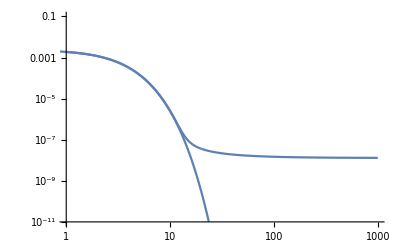

comentario: a medida que subo el valor de los λ desde 10 a la 8 hasta 10 a la 12, se vuelve cada vez mas torpe. Sin embargo es critico que la ecuacion barra estos valores. ¿ayudaria dividir en más segmentos el dominio? esto puede hacerse de forma más eficieente con un ciclo... que ciclo?? debo estudiar programacion basica....